```mathematica
n = Input["Input коллическво работ",]
```

1

```mathematica
T = {}
Do[T = Append [T,Input["Input",{,,{}}]], {i, 1, n, 1}](*Ввод данных в формате {Работа,Длительность,{Предшественники}}*)
```

{}

```mathematica
T ={{1,,{}},{2,,{}},{3,,{2}},{4,,{3}},{5,,{1,3}},{6,,{4}},{7,,{2}},{8,,{6}}}
```

{{1,Null,{}},{2,Null,{}},{3,Null,{2}},{4,Null,{3}},{5,Null,{1,3}},{6,Null,{4}},{7,Null,{2}},{8,Null,{6}}}

```mathematica
e = {}
v = {}
Do[ Do[ e = Append[e,T[[i]][[1]] ->T[[i]][[3]][[j]]], {j, 1, Length[T[[i]][[3]]], 1}], {i, 1,Length[T], 1}](*Задание графа по списку ребер*)
Do[v= Append[v,T[[i]][[1]]], {i, 1, Length[T], 1}](*Вершины*)
e
```

{}

{}

{3->2,4->3,5->1,5->3,6->4,7->2,8->6}

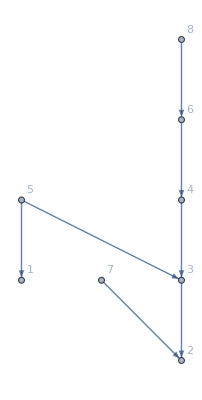

```mathematica
g  = Graph[v,e, VertexLabels -> "Name"](*Прорисовка графа*)
```

```mathematica
mat = Table[AdjacencyMatrix[g]](*Матрица смежности*)
```

SparseArray[…]

```mathematica
MatrixForm[mat]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
Do[ Do[If [mat[[i,k]]==1,Do[mat[[i,j]] = If[(mat[[i,j]] + mat[[k,j]]) >0,1,0],{j, 1,Length[T]}]] ,{i , 1,Length[T]}],{k, 1,Length[T]}](*Матрица достижимости*)
```

```mathematica
MatrixForm[mat]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0)

```mathematica
l = {Normal[mat[[1]]]}
k = {{1}}
Do[ If[Count [l, Normal[mat[[i]]]]== 0,l = Append[l,Normal[mat[[i]]]] ;k = Append[k,{i}] ,k[[Position [l, Normal[mat[[i]]]][[1]][[1]]]] = Append[k[[Position [l, Normal[mat[[i]]]][[1]][[1]]]],i]], {i, 2,Length[T], 1}]
l(*Уникальные строки*)
k(*Значения Пи *)
```

{{0,0,0,0,0,0,0,0}}

{{1}}

{{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,1,0,0,0,0,0},{1,1,1,0,0,0,0,0},{0,1,1,1,0,0,0,0},{0,1,1,1,0,1,0,0}}

{{1,2},{3,7},{4},{5},{6},{8}}

```mathematica
mattrans = Transpose[mat](*Транспонированная матрица достижимости*)
```

SparseArray[…]

```mathematica
l1 = {Normal[mattrans[[1]]]}
k1 = {{1}}
Do[ If[Count [l1, Normal[mattrans[[i]]]]== 0,l1 = Append[l1,Normal[mattrans[[i]]]] ;k1 = Append[k1,{i}] ,k1[[Position [l1, Normal[mattrans[[i]]]][[1]][[1]]]] = Append[k1[[Position [l1, Normal[mattrans[[i]]]][[1]][[1]]]],i]], {i, 2,Length[T], 1}]
l1(*Уникальные столбцы*)
k1(*Значения p*)
```

{{0,0,0,0,1,0,0,0}}

{{1}}

{{0,0,0,0,1,0,0,0},{0,0,1,1,1,1,1,1},{0,0,0,1,1,1,0,1},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1}}

{{1},{2},{3},{4},{5,7,8},{6}}

```mathematica
e1 ={}
Do[ Do[ e1 = Append[e1,Position[k,k[[i]]][[1]][[1]]->(Position[k1,k[[i]][[j]]][[1]][[1]] +Length[k])] , {j, 1, Length[k[[i]]], 1}], {i, 1,Length[k], 1}]
e1(*Пути из Пи в p*)
```

{}

{1->7,1->8,2->9,2->11,3->10,4->11,5->12,6->11}

```mathematica
e2 = {}
Do[ Do[ If[MemberQ[Position[l[[j]],1],{i}],e2= Append[e2,(i +Length[k]) ->Position[l,l[[j]]][[1]][[1]]]], {j, 1, Length[k], 1}], {i, 1,Length[k1], 1}]
e2(*Пути p в Пи*)
```

Thread::tdlen: Objects of unequal length in {} Null {7->4,8->2,8->3,8->4,8->5,8->6,9->3,9->4,9->5,9->6,10->5,10->6,12->6} cannot be combined.

Null {} {7->4,8->2,8->3,8->4,8->5,8->6,9->3,9->4,9->5,9->6,10->5,10->6,12->6}

```mathematica
e2
```

{7->4,8->2,8->3,8->4,8->5,8->6,9->3,9->4,9->5,9->6,10->5,10->6,12->6}

```mathematica
ekon =Join[ e1 , e2](*Обьединяем пути для создания графа*)
```

{1->7,1->8,2->9,2->11,3->10,4->11,5->12,6->11,7->4,8->2,8->3,8->4,8->5,8->6,9->3,9->4,9->5,9->6,10->5,10->6,12->6}

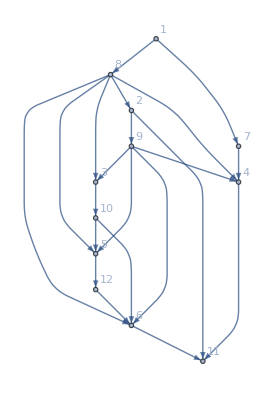

```mathematica
g1 = Graph[ekon, VertexLabels -> "Name"](*Прорисовка графа*)
```